```mathematica
SetDirectory["~/Documents/research/tidal_dynamics/dgdlnrp_tables_Faber/"]
```

/Users/linda/Documents/research/tidal_dynamics/dgdlnrp_tables_Faber

```mathematica
<<596.dgdlnrp;
rate596=rate;
```

```mathematica
<<4434.dgdlnrp;
rate4434=rate;
```

```mathematica
<<4464.dgdlnrp;
rate4464=rate;
```

```mathematica
<<4467.dgdlnrp;
rate4467=rate;
```

```mathematica
<<4564.dgdlnrp;
rate4564=rate;
```

```mathematica
<<4742.dgdlnrp;
rate4742=rate;
```

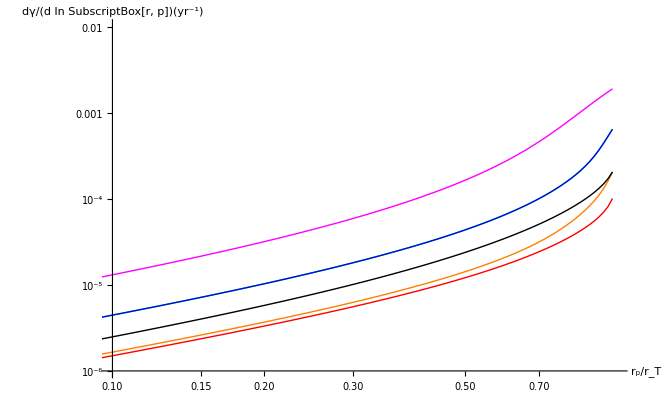

```mathematica
ListLogLogPlot[{rate596,rate4434,rate4464,rate4467,rate4564,rate4742},Joined->True,PlotStyle->{{Red,Thick},{Orange,Thick},{Green,Thick},{Blue,Thick},{Black,Thick},{Magenta,Thick}},
AxesStyle->{Thick,Thick},LabelStyle->{FontSize->18,FontWeight->"Bold"},PlotRange->{{.1,1},{10^-6,10^-2}},AxesLabel->{"\!\(\*FractionBox[SubscriptBox[\(r\), \(p\)], SubscriptBox[\(r\), \(T\)]]\)","\!\(\*FractionBox[\(dγ\), \(d\\\ ln\\\ \*SubscriptBox[\(r\), \(p\)]\)]\)(\!\(\*SuperscriptBox[\(yr\), \(-1\)]\))"}]
```

```mathematica
norm596=Partition[Riffle[rate596[[All,1]],rate596[[All,2]]/rate596[[33,2]]],2];
norm4434=Partition[Riffle[rate4434[[All,1]],rate4434[[All,2]]/rate4434[[33,2]]],2];
norm4464=Partition[Riffle[rate4464[[All,1]],rate4464[[All,2]]/rate4464[[33,2]]],2];
norm4467=Partition[Riffle[rate4467[[All,1]],rate4467[[All,2]]/rate4467[[33,2]]],2];
norm4564=Partition[Riffle[rate4564[[All,1]],rate4564[[All,2]]/rate4564[[33,2]]],2];
norm4742=Partition[Riffle[rate4742[[All,1]],rate4742[[All,2]]/rate4742[[33,2]]],2];
```

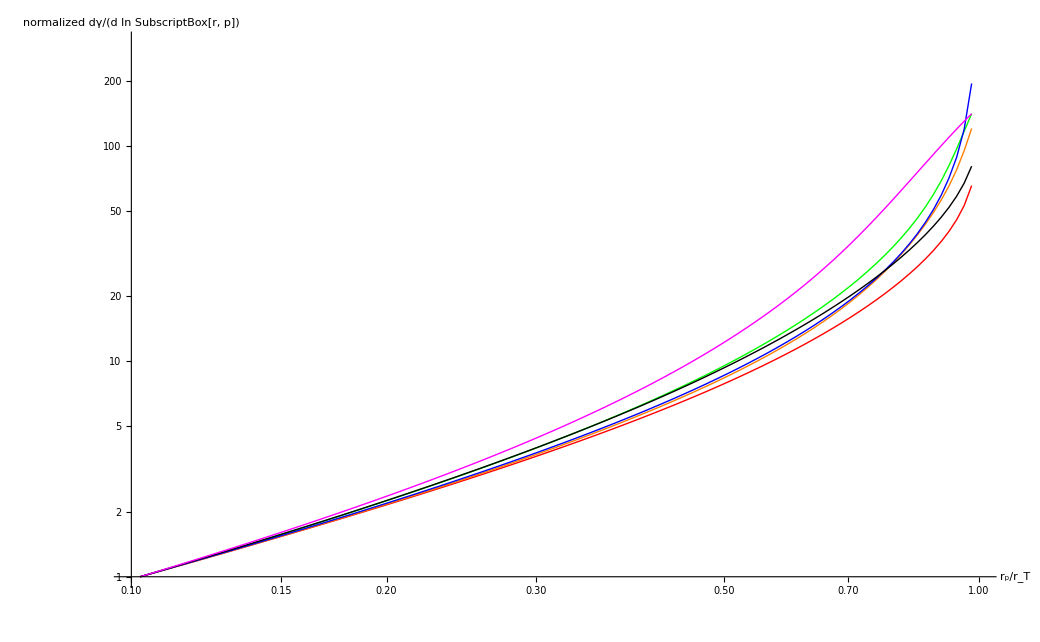

```mathematica
Print[ListLogLogPlot[{norm596,norm4434,norm4464,norm4467,norm4564,norm4742},Joined->True,PlotStyle->{Red,Orange,Green,Blue,Black,Magenta},PlotRange->{{0.1,1},{1,300}},
AxesStyle->{Thick,Thick},PlotStyle->{Thick,Black},LabelStyle->{FontSize->18,FontWeight->"Bold"},AxesLabel->{"\!\(\*FractionBox[SubscriptBox[\(r\), \(p\)], SubscriptBox[\(r\), \(T\)]]\)","normalized \!\(\*FractionBox[\(dγ\), \(d\\\ ln\\\ \*SubscriptBox[\(r\), \(p\)]\)]\)"}]];
```